```mathematica
zMin:=-10
zMax:=22
m:=10
```

```mathematica
solutions=NDSolve[{ϕ'[z]/(ϕ[z]ϕ[z]*)^2==-(ϕ[z]*)^2 Log[((ϕ[z]*)^3(χ[z]*)^2)/1],χ'[z]/(χ[z]χ[z]*)^2==-χ[z]*((4(ϕ[z]*)^3)/(3(χ[z]*)^2)-m), ϕ[zMax]^3==(√(3m))/2,χ[zMax]^2==2/(√(3m))}, {ϕ[z], χ[z]}, {z, zMin, zMax}]
```

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

NDSolve::mconly: For the method NDSolve`IDA, only machine real code is available. Unable to continue with complex values or beyond floating-point exceptions.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

NDSolve::mconly: For the method NDSolve`IDA, only machine real code is available. Unable to continue with complex values or beyond floating-point exceptions.

General::stop: Further output of NDSolve::mconly will be suppressed during this calculation.

{{ϕ[z]→InterpolatingFunction[…][z],χ[z]→InterpolatingFunction[…][z]},{ϕ[z]→InterpolatingFunction[…][z],χ[z]→InterpolatingFunction[…][z]}}

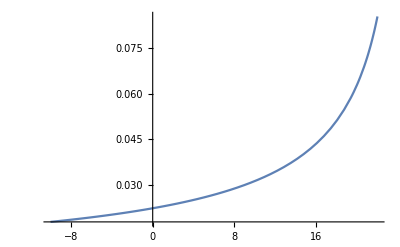

```mathematica
Plot[Evaluate[ϕ[z]/.solutions[[1]]]^3, {z, zMin, zMax}, PlotRange->All]
```

```mathematica
NDSolve[{ϕ'[z]==-(ϕ[z]*)^2 Log[((ϕ[z]*)^3(χ[z]*)^2)/1],χ'[z]==-χ[z]*((4(ϕ[z]*)^3)/(3(χ[z]*)^2)-1), ϕ[zMax]^3==(√3)/2,χ[zMax]^2==2/(√3)}, {ϕ[z], χ[z]}, {z, zMin, zMax}]
```

```mathematica
NDSolve[{ϕ'[z]==-2 m^(1/6)ϕ[z]^2 Log[ϕ[z]^3 χ[z]^2], χ'[z]==m χ[z](1-(4 ϕ[z]^3)/(3 χ[z]^2)), ϕ[zMax]^3==(√(3m))/2, ϕ'[zMax]==0, χ'[zMax]==0,χ[zMax]^2==2/(√(3m))}, {ϕ[z], χ[z]},{z, zMin, zMax}]
```

NDSolve::ivcon: The given initial conditions were not consistent with the differential-algebraic equations. NDSolve will attempt to correct the values.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

NDSolve::ndsz: At z == 21.9565, step size is effectively zero; singularity or stiff system suspected.

NDSolve::mconly: For the method NDSolve`IDA, only machine real code is available. Unable to continue with complex values or beyond floating-point exceptions.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

NDSolve::ndsz: At z == 21.9565, step size is effectively zero; singularity or stiff system suspected.

NDSolve::mconly: For the method NDSolve`IDA, only machine real code is available. Unable to continue with complex values or beyond floating-point exceptions.

General::stop: Further output of NDSolve::mconly will be suppressed during this calculation.

{{ϕ[z]→InterpolatingFunction[…][z],χ[z]→InterpolatingFunction[…][z]},{ϕ[z]→InterpolatingFunction[…][z],χ[z]→InterpolatingFunction[…][z]}}